```mathematica
ClearAll[Ausgleichsgerade];
Ausgleichsgerade[xValues_,yValues_]:=(
If[Length[xValues]==Length[xValues],,Throw["Arrays sind nicht gleich lang"]
];
ClearAll[n,xxValues,xyValues,Δ,xSum,ySum,xxSum,xySum,a,b,s2,σa,σb,Δc,r,yTrue,σy];

n=Length[xValues];

xxValues=Table[xValues[[i]]^2,{i,1,n}];
xyValues=Table[xValues[[i]]*yValues[[i]],{i,1,n}];

xSum=Sum[xValues[[i]],{i,1,n}];
ySum=Sum[yValues[[i]],{i,1,n}];
xxSum=Sum[xxValues[[i]],{i,1,n}];
xySum=Sum[xyValues[[i]],{i,1,n}];

Δ=n*xxSum-xSum^2;
a=1/Δ*(xxSum*ySum-xSum*xySum);
b=1/Δ*(n*xySum-xSum*ySum);

r=(n*xySum-xSum*ySum)/(√((n*xxSum-xSum^2)*(n*Sum[yValues[[i]]^2,{i,1,n}]-ySum^2)));

s2=1/(n-2)*Sum[(yValues[[i]]-a-b*xValues[[i]])^2,{i,1,n}];
σa=√(s2/Δ*xxSum);
σb=√(n*s2/Δ);

x=xSum/n;
y=ySum/n;
Δc=√(x^2*σb^2+σa^2);

yTrue=Table[b*xValues[[i]]+a,{i,1,n}];
σy=Table[(yValues[[i]]-yTrue[[i]])^2,{i,1,n}];
yTrueSum:=Sum[yTrue[[i]],{i,1,n}];
σySum:=Sum[σy[[i]],{i,1,n}];

Print["\n",TableForm[{Join[xValues,{"",xSum}],Join[yValues,{"",ySum}],Join[yTrue,{"",yTrueSum}],Join[σy,{"",σySum}],Join[xxValues,{"",xxSum}],Join[xyValues,{"",xySum}]},TableDirections->Row,TableSpacing->{3, 1},TableHeadings->{{"x_i", "y_i","y","(y-y_i)^2","x_i^2","x_i*y_i" },Join[Table["",{i,1,n+1}],{"Sum:"}]}]];
Print["\n","a = ",a," ± ",σa,"\n","b = ",b," ± ",σb,"\n","r = ",r,"\n","x̄ = ",x,"; ȳ = ",y,"; Δc = ",Δc];
Print["\n","=> y = (b ± Δb)*(x - x̄) + (ȳ ± Δc)","\n","=> y = (",b," ± ",σb,")*(x - ",x,") + ",y," ± ",Δc];
Show[{
ListPlot[Table[{xValues[[i]],yValues[[i]]},{i,1,n}],PlotStyle->Red,PlotMarkers->"X"],
Plot[{
(b)*(xCoord-x)+y,
(b+σb)*(xCoord-x)+y+Δc,
(b-σb)*(xCoord-x)+y+Δc,
(b+σb)*(xCoord-x)+y-Δc,
(b-σb)*(xCoord-x)+y-Δc
},
{xCoord,Floor[First[xValues]],Ceiling[Last[xValues]]},
PlotStyle->{Automatic,RGBColor[169/256,195/256,97/256,0.7],RGBColor[169/256,195/256,97/256,0.7],RGBColor[230/256,171/256,68/256,0.7],RGBColor[230/256,171/256,68/256,0.7]}
]
},ImageSize->Full]
)
```

| x_i | y_i | y | (y-y_i)^2 | x_i^2 | x_i*y_i
 | 0.27 | 3.48 | 3.37061 | 0.0119668 | 0.0729 | 0.9396
 | 0.89 | 3.6 | 3.5183 | 0.0066747 | 0.7921 | 3.204
 | 1.99 | 3.71 | 3.78034 | 0.00494757 | 3.9601 | 7.3829
 | 3.04 | 3.92 | 4.03047 | 0.0122027 | 9.2416 | 11.9168
 | 3.81 | 4.06 | 4.21389 | 0.0236829 | 14.5161 | 15.4686
 | 5.1 | 4.51 | 4.52119 | 0.000125248 | 26.01 | 23.001
 | 5.82 | 4.79 | 4.69271 | 0.00946591 | 33.8724 | 27.8778
 | 6.97 | 4.98 | 4.96666 | 0.000178069 | 48.5809 | 34.7106
 | 8.1 | 5.28 | 5.23584 | 0.0019501 | 65.61 | 42.768
 |  |  |  |  |  | 
Sum: | 35.99 | 38.33 | 38.33 | 0.0711941 | 202.656 | 167.269

a = 3.30629 ± 0.0624423
b = 0.238216 ± 0.0131589
r = 0.989488
x̄ = 3.99889; ȳ = 4.25889; Δc = 0.0816579

=> y = (b ± Δb)*(x - x̄) + (ȳ ± Δc)
=> y = (0.238216 ± 0.0131589)*(x - 3.99889) + 4.25889 ± 0.0816579

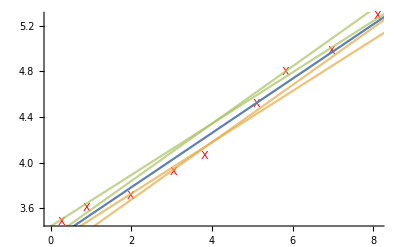

```mathematica
(*xValues={0.20,1.17,1.96,2.98,4.05,5.12,5.93,7.01,8.24};
yValues={52.4,54.6,57.7,59.5,62.7,65.6,67.0,69.0,72.8};*)

(*xValues={0.23,0.96,2.18,3.03,3.84,4.98,6.10,7.19,8.29};
yValues={-73.5,-71.0,-68.9,-66.7,-65.8,-64.1,-61.5,-58.7,-55.1};*)

xValues={0.27,0.89,1.99,3.04,3.81,5.1,5.82,6.97,8.1};
yValues={3.48,3.6,3.71,3.92,4.06,4.51,4.79,4.98,5.28};

Ausgleichsgerade[xValues,yValues]
```